# Otimização Geométrica de Linhas de Transmissão

## Robson Dias - COPPE/UFRJ

Este programa faz a otimização da configuração geometrica dos condutores da Linha de Transmissão, após realizada a otimização dos condutores. Este programa está dividido em duas partes a primeira são definidas as restrições do problema e a segunda a otimização propriamente dita. Não comtempla os cabos PR

## Inicialização

```mathematica
hj=Date[];
Print[hj[[3]],"/ ",hj[[2]],"/ ",hj[[1]]]
Print[" às ", hj[[4]], ":",hj[[5]]]
```

3/ 8/ 2018

às 15:17

```mathematica
SetDirectory[NotebookDirectory[]]
(*SetDirectory["B:\\otlin"]*)
```

C:\Users\Usuário\Dropbox\TBE_calc_param\analise_tunico_cabos_ACSR\1700MVA\bonding_4_por_fase

```mathematica
dadoscond=Import["condcompleta.txt","Table"];
camp=Import["campos.txt","CSV"];
```

## Variáveis obtidas do programa de otimização dos condutores

```mathematica
nfase=3;
ns=4;
npr=2;
ncond=IntegerPart[ns*nfase+npr]
```

14

### Dados do Meio

#### Ar

```mathematica
μo=4.0*Pi*10^-7;
ϵo=1.0/(36*π*10^9);
```

#### Solo

```mathematica
σearth=10^-3;                                 (* ⟹ Condutividade do Solo ⟸ *)
```

### Dados do condutor

```mathematica
Nome=ToUpperCase["grackle"];
```

```mathematica
pos=Module[{posicao},posicao=If[NumberQ[Position[dadoscond,Nome][[1,1]]],Position[dadoscond,Nome][[1,1]],1];If[NumberQ[Position[dadoscond,Nome][[1,1]]],,Print["O condutor especificado não exite na tabela, verifique o nome digitado. Para não ocorrer erros nos cálculos foram utilizados os valores do condutor Owl"]];Return[posicao]];

{nome,MCM,NAl,DAl,NACO,DACO,secAl,secACO,Dcond,DALMA,PesoAl,PesoACO,Massa,CargaRupturaClasseA,CargaRupturaClasseB,Ampacidade,RMG,ResCC,ResAC,Xind,Xcap}=dadoscond[[pos]];

Table[Print[i,")  ",camp[[i,1]], " = ",dadoscond[[pos,i]]],{i,1,Length[camp]}];
```

Return[52]

1)  Nome comercial = GRACKLE

2)  Bitola (MCM) = 1192.5

3)  Num. de Fios de Al. = 54

4)  Diâmetro dos Fios de Al. (mm) = 3.774

5)  Num. de Fios de Aço = 19

6)  Diâmetro dos Fios de Aço (mm) = 2.266

7)  Seção transversal de Al (mm^2) = 604.07

8)  Seção transversal do cond. (mm^2) = 680.7

9)  Diâmetro do cond. (mm) = 33.97

10)  Diâmetro da Alma de Aço (mm) = 11.33

11)  Peso Nominal do Al (aprox.) (kg/km) = 1681.8

12)  Peso nominal do Aço (aprox.) (kg/km) = 599.7

13)  Massa (aprox.) (kg/km) = 2281.5

14)  Carga de ruptura (Classe A) (kgf) = 18987

15)  Carga de ruptura (Classe B) (kgf) = 18478

16)  Ampacidade (A) = 1140

17)  Raio médio geométrico (m) = 0.01376

18)  Resistência elétrica máxima CC a 20.baC (Ohm/km) = 0.048

19)  Resistência elétrica máxima CA @ 60 Hz e 75.baC (Ohm/km) = 0.056

20)  Reatância indutiva (Ohm/km) = 0.3232

21)  Reatância capacitiva (Mohm/km) = 0.1945

### Dados dos Condutores

```mathematica
r0=(dadoscond[[pos,10]]/2)*10^-3;   (* ⟹ [m] ⟸ *)
r1=(dadoscond[[pos,9]]/2)*10^-3;

ρAl=0.028264;    (* resistividade ⟹ Ω × mm^2/ m ⟸ *)
ρAlmetro=0.028264*10^-6;    (* ⟹ Ω × m ⟸ *)

Rdcϕ=(dadoscond[[pos,18]])*10^-3;  (* ⟹ [Ω/m] ⟸⟹ @ 20^o ⟸*)
ρϕ=Rdcϕ*Pi*(r1^2-r0^2);

σϕ=(1/ρAlmetro)*(dadoscond[[pos,3]]*(dadoscond[[pos,4]]*10^-3/2)^2)/(r1^2-r0^2);
```

```mathematica
svao=0.5; (* comprimento do vão em [km] *)
T=dadoscond[[pos,15]];
W=dadoscond[[pos,13]];
H=0.24*T;
Ccat=H/W;
(*flecha em metro
flechacond=1000*Ccat*(Cosh[svao/(2*Ccat)]-1)*)
flechacond=0.0
```

0.

### Dados dos Cabos PR

```mathematica
rpr=4.57*10^-3; (* [m] *)

Rdcpr=4.19*10^-3;

ρpr=Rdcpr*Pi*rpr^2;

σpr=1/ρpr;

μpr=80*μo;
```

```mathematica
Tpr=6980; (*{kgf]*)
Wpr=410; (*[kg/km]*)
Hpr=0.25*Tpr;
Ccatpr=Hpr/Wpr;
(*flecha em metro
flechapr=1000*Ccatpr*(Cosh[svao/(2*Ccatpr)]-1)*)
flechapr=0.0;
```

#### Lista de raios dos condutores

```mathematica
r=Join[Table[r1,{ncond-npr}],Table[rpr,{npr}]];
```

## Restrições

### Definição das variáveis a serem otimizadas (coordenadas dos condutores na torre)

```mathematica
varx=Array[ToExpression[StringJoin["coorx",ToString[#]]]&,ncond];
vary=Array[ToExpression[StringJoin["coory",ToString[#]]]&,ncond];
```

## Definição da Funçao Objetivo e Otimização

### Dados

```mathematica
(*== Tensão Fase-Neutro (kV) ==*)
NU1=500./Sqrt[3]; 

(*== Potência Característica (MW) ==*)
NPc=1700.0;                     

nfase=3;

(* Densidade de Corrente *)
NJc=0.82;                     

(* Fator de Preenchimento *)
Npreen=0.7;                

(* Fator de Utilização *)
Nku= 0.95;                    

(* Altura  [m] *)
Nh=100;

(* temperatura do Cond [°C]*)

Ntemp=60;

(* temperatura do Ar [°C]*)

NtempAr=40;

(* Fator de Superfície *)
Nm=0.82;                       

(* Tolerância *)
Ntol=3*10^-2;
```

## Coordenadas iniciais

```mathematica
rxint=ryint=rxext=ryext=1.25;
```

```mathematica
(*Distância Mínima entre condutores de fases distintas*)
dmin=10;
```

```mathematica
cx={-(rxext+rxint+dmin),0.};

(*Altura do centro na torre, flecha + o raio do feixe + altura mínima (hmin, na verdade, está altura corresponde a altura mínima até a extremidade do raio, mas para valor inicial serve*)

hmin=16;
cy=flechacond+ryext+{hmin,hmin+1.0};
```

```mathematica
dminpr=9;
xpr=15.0;

ypr=flechacond+2*ryext+hmin+dminpr;
```

```mathematica
{cxext,cxint}=N[{cx[[1]],cx[[2]]}];
{cyext,cyint}=N[{cy[[1]],cy[[2]]}];

coornspar[ns_]:=Module[{temp},
temp=Join[Array[{cxext+(rxext*Sin[Pi/ns+(#-1)*2.0*Pi/ns]),cyext-ryext*Cos[Pi/ns+(#-1)*2.0*Pi/ns]}&,ns],Array[{cxint+(rxint*Sin[Pi/ns+(#-1)*2.0*Pi/ns]),cyint-ryint*Cos[Pi/ns+(#-1)*2.0*Pi/ns]}&,ns],Array[{-cxext+(rxext*Sin[Pi/ns+(#-1)*2.0*Pi/ns]),cyext-ryext*Cos[Pi/ns+(#-1)*2.0*Pi/ns]}&,ns]];
{temp[[All,1]],temp[[All,2]]}];

{xini,yini}=Module[{xi,yi},{xi,yi}=coornspar[ns];
If[npr==2,{Join[xi,{-xpr,xpr}],Join[yi,{ypr,ypr}]},If[npr==1,{Join[xi,{xpr}],Join[yi,{ypr}]},{xi,yi}]]];
```

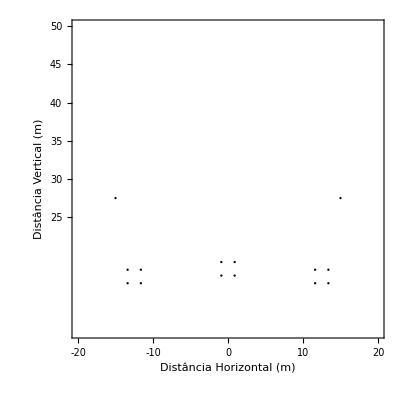

```mathematica
torre=Show[Graphics[{Disk[{xini[[#]],yini[[#]]},0.15]&/@Range[ncond]}],PlotRange->{{-20,20},{10,50}},Frame->True,
FrameTicks->{Table[i,{i,-20,20,5}],Table[i,{i,25,50,5}],None,None},
FrameLabel->{"Distância Horizontal (m)", "Distância Vertical (m)"},
LabelStyle->12,
FrameStyle->AbsoluteThickness[1.],
AspectRatio->Automatic]
```

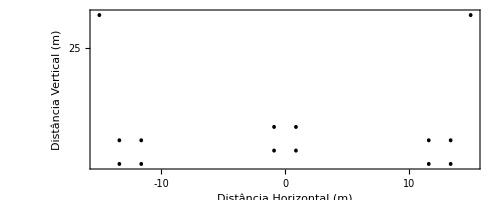

```mathematica
Show[Graphics[{Disk[{xini[[#]],yini[[#]]},0.15]&/@Range[ncond]}],Frame->True,
FrameTicks->{Table[i,{i,-20,20,5}],Table[i,{i,25,50,5}],None,None},
FrameLabel->{"Distância Horizontal (m)", "Distância Vertical (m)"},
LabelStyle->12,
FrameStyle->AbsoluteThickness[1.],
AspectRatio->Automatic]
```

```mathematica
TableForm[Transpose@{Table[i,{i,ncond}],xini,yini}]
```

1 | -11.6161 | 16.3661
2 | -11.6161 | 18.1339
3 | -13.3839 | 18.1339
4 | -13.3839 | 16.3661
5 | 0.883883 | 17.3661
6 | 0.883883 | 19.1339
7 | -0.883883 | 19.1339
8 | -0.883883 | 17.3661
9 | 13.3839 | 16.3661
10 | 13.3839 | 18.1339
11 | 11.6161 | 18.1339
12 | 11.6161 | 16.3661
13 | -15. | 27.5
14 | 15. | 27.5

### Densidade Relativa e Campo Crítico

```mathematica
δ1[h_,t_]:=0.28924*(1013*Exp[-0.116*(h/1000)])/(273+t);
(* Apostila do Portela *)
```

```mathematica
EcrPortela[r_,h_,t_,m_]:=Module[{Ec,Ecm,Ecr,A1,A0,raux},
A0=829.7;
A1=781.53;
Ec=2.4381;
Ecm=Ecr/(m*δ1[h,t]);
raux=r*δ1[h,t];

(*resultado é dado em MV/m e em valor Pico*)

Ecr/.FindRoot[-A0*(Ecm/Ec-1)^2+A1*Ecm*(Ecm/Ec-1-Log[Ecm/Ec])==1/raux,{Ecr,Ec}]];
```

```mathematica
EcrCond=EcrPortela[r1,Nh,Ntemp,Nm]*10/Sqrt[2];
EcrPr=EcrPortela[rpr,Nh,NtempAr,Nm]*10/Sqrt[2];
Print["Campo Elétrico Crítico Cond"," = ",EcrCond," kV/cm"];
Print["Campo Elétrico Crítico PR"," = ",EcrPr," kV/cm"]
```

Campo Elétrico Crítico Cond = 18.6379 kV/cm

Campo Elétrico Crítico PR = 24.3613 kV/cm

### Campo Elétrico Superficial

### Determinação da Matriz de Potenciais de Maxwell (Númerica e Simbólica)

```mathematica
PNum[xx1_List?(Union[Map[NumberQ,#]][[1]]&),yy1_List?(Union[Map[NumberQ,#]][[1]]&)]:=Module[{pp},
pp=1/(2*Pi*ϵo)*Log[Table[If[i==j,2*yy1[[i]]/r[[i]],(Sqrt[(yy1[[i]]+yy1[[j]])^2+(xx1[[i]]-xx1[[j]])^2]/Sqrt[(yy1[[i]]-yy1[[j]])^2+(xx1[[i]]-xx1[[j]])^2])],{i,1,ncond},{j,1,ncond}]];Return[pp]];
```

```mathematica
PSym[xx2_List,yy2_List]:=Module[{pp},
pp=1/(2*Pi*ϵo)*Log[Table[If[i==j,2*yy2[[i]]/r[[i]],(Sqrt[(yy2[[i]]+yy2[[j]])^2+(xx2[[i]]-xx2[[j]])^2]/Sqrt[(yy2[[i]]-yy2[[j]])^2+(xx2[[i]]-xx2[[j]])^2])],{i,1,ncond},{j,1,ncond}]];Return[pp]];
```

#### Vetor de tensões, considerando os cabos PR aterrados em todas as torres

```mathematica
MU=(NU1*10^3)*Join[Flatten[Table[Exp[-(ⅈ*2*π/nfase)*#],{ns}]&/@Range[0,nfase-1]],Table[0,{npr}]];
```

#### Calculo das cargas nos condutores

```mathematica
qtotal[xx3_List?(Union[Map[NumberQ,#]][[1]]&),yy3_List?(Union[Map[NumberQ,#]][[1]]&)]:=Module[{q},
(*as tensões devem estar em Volts *)
q=Inverse[PSym[xx3,yy3]].MU; Return[q]]
```

#### Campos Superficiais Máximos

```mathematica
Esupmax[xx4_List?(Union[Map[NumberQ,#]][[1]]&),yy4_List?(Union[Map[NumberQ,#]][[1]]&)]:=Module[{Nq,C00,campos,camposmax,camposmaxmax,γ,ang},

ang[i_,j_]:=Module[{},If[j<=ncond,If[i==j,0,ArcTan[xx4[[j]]-xx4[[i]],yy4[[j]]-yy4[[i]]]],If[i==j,-π/2,ArcTan[xx4[[j-ncond]]-xx4[[i]],yy4[[j-ncond]]+yy4[[i]]]]]];

Nq=qtotal[xx4,yy4];

C00=Table[(Nq[[i]]/(2*π*ϵo*r[[i]])),{i,Length[Nq]}];

campos=Table[C00[[i]]+Sum[Sum[If[k==i,0,If[k<=ncond,-2*Nq[[i]]/(2*π*ϵo*r[[i]])*(r[[i]]/Sqrt[(yy4[[i]]-yy4[[k]])^2+(xx4[[i]]-xx4[[k]])^2])^h*Cos[γ-ang[i,k]],2*Nq[[k-ncond]]/(2*π*ϵo*r[[i]])*(r[[i]]/Sqrt[(yy4[[i]]+yy4[[k-ncond]])^2+(xx4[[i]]-xx4[[k-ncond]])^2])^h*Cos[γ-ang[i,k]]]],{k,1,2*ncond}],{h,1,2}],{i,ncond}];

 camposmax=Table[FindMinimum[-Abs[campos[[i]]],{γ,0,2*π}],{i,Length[campos]}];

camposmaxmax=Max[-camposmax[[All,1]]]*10^-5;Return[-camposmax[[All,1]]*10^-5]]
```

```mathematica
EsupmaxInd[posi_,xx5_List?(Union[Map[NumberQ,#]][[1]]&)]:=Block[{xEmax,yEmax,ytemp,pts,Nq,C00,campos,camposmax,camposmaxmax,γ,ang},

pts=Thread[varsym->xx5];

xEmax=varx/.pts;

(*O campo é crítico no meio do vão*)

ytemp=vary/.pts;

yEmax=Table[If[i<=ncond-npr,ytemp[[i]]-flechacond,ytemp[[i]]-flechapr],{i,ncond}];

ang[i_,j_]:=Module[{},If[j<=ncond,If[i==j,0,ArcTan[xEmax[[j]]-xEmax[[i]],yEmax[[j]]-yEmax[[i]]]],If[i==j,-π/2,ArcTan[xEmax[[j-ncond]]-xEmax[[i]],yEmax[[j-ncond]]+yEmax[[i]]]]]];

Nq=qtotal[xEmax,yEmax];

C00=Table[(Nq[[i]]/(2*π*ϵo*r[[i]])),{i,Length[Nq]}];

campos=Table[C00[[i]]+Sum[Sum[If[k==i,0,If[k<=ncond,-2*Nq[[i]]/(2*π*ϵo*r[[i]])*(r[[i]]/Sqrt[(yEmax[[i]]-yEmax[[k]])^2+(xEmax[[i]]-xEmax[[k]])^2])^h*Cos[γ-ang[i,k]],2*Nq[[k-ncond]]/(2*π*ϵo*r[[i]])*(r[[i]]/Sqrt[(yEmax[[i]]+yEmax[[k-ncond]])^2+(xEmax[[i]]-xEmax[[k-ncond]])^2])^h*Cos[γ-ang[i,k]]]],{k,1,2*ncond}],{h,1,2}],{i,ncond}];

 camposmax=Table[FindMinimum[-Abs[campos[[i]]],{γ,0,2*π}],{i,Length[campos]}];
Return[-camposmax[[posi,1]]*10^-5]]
```

```mathematica
yini2=Table[If[i<=ncond-npr,yini[[i]]-flechacond,yini[[i]]-flechapr],{i,ncond}];
```

```mathematica
Esupmaxini=Esupmax[xini,yini2];
Ecrtodos=Table[If[i<=ncond-npr,EcrCond,EcrPr],{i,ncond}];

fatorEc=Esupmaxini[[#]]/Ecrtodos[[#]]&/@Range[ncond];
```

```mathematica
Esolo[xsolo_,ysolo_,xx_List?(Union[Map[NumberQ,#]][[1]]&),yy_List?(Union[Map[NumberQ,#]][[1]]&)]:=Module[{Nq,Esolo},
Nq=qtotal[xx,yy];

Esolo=Sum[(Nq[[k]]/(2*π*ϵo))*((xsolo-xx[[k]])*(1/((xsolo-xx[[k]])^2+(ysolo-yy[[k]])^2)-1/((xsolo-xx[[k]])^2+(ysolo+yy[[k]])^2))+ⅈ*((ysolo-yy[[k]])/((xsolo-xx[[k]])^2+(ysolo-yy[[k]])^2)-(ysolo+yy[[k]])/((xsolo-xx[[k]])^2+(ysolo+yy[[k]])^2))),{k,Length[xx]}];

Return[Esolo]]
```

```mathematica
TableForm[Transpose[{Join[{"N°"},Range[Length[varx]]],Join[{"Emax (kV/cm)"},Esupmaxini],Join[{"Emax/Ec"},fatorEc]}]]
```

N° | Emax (kV/cm) | Emax/Ec
1 | 14.5009 | 0.77803
2 | 14.4921 | 0.777562
3 | 13.792 | 0.739995
4 | 13.7896 | 0.739866
5 | 15.4309 | 0.82793
6 | 15.2542 | 0.818447
7 | 15.2542 | 0.818447
8 | 15.4309 | 0.82793
9 | 13.7896 | 0.739866
10 | 13.792 | 0.739995
11 | 14.4921 | 0.777562
12 | 14.5009 | 0.77803
13 | 16.2377 | 0.666538
14 | 16.2377 | 0.666538

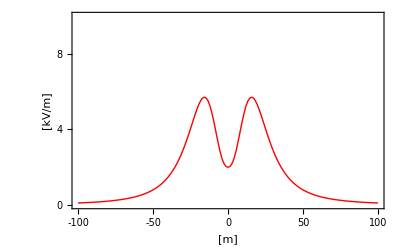

```mathematica
CampoSolo=Plot[Abs[Esolo[x,1,xini,yini2]]/1000,{x,-100,100},
PlotRange->{{-100,100},{0,10}},
PlotStyle->{RGBColor[1,0,0],AbsoluteThickness[1]},
Axes->False,
FrameTicks->{Table[i,{i,-100,100,25}],Table[i,{i,0,16,2}],None,None},Frame->True,FrameLabel->{"[m]", "[kV/m]"},LabelStyle->12,
FrameStyle->AbsoluteThickness[1.]]
```

```mathematica
(*Export["Esolo500kVB.pdf",CampoSolo,"PDF"]*)
```

## Inicio da Otimização

### Carga Admissível

```mathematica
qad[raios_,h_,t_,m_]:=2*π*ϵo*raios*EcrPortela[raios,h,t,m]*(10^6)/Sqrt[2]; (* 10^6 ⟹ MV/m para Volt/m e 1/√2 valor rms*)
Nqad=qad[r1,Nh,Ntemp,Nm]
```

1.75869×10^-6

### Variáveis de otimização

```mathematica
varelipse={xcExt,ycExt,RxRyExt2,RxExt2,xcInt,ycInt,RxRyInt2,RxInt2};
ptsinielipse={cx[[1]],cy[[1]],(rxext/ryext)^2,rxext^2,cx[[2]],cy[[2]],(rxint/ryint)^2,rxint^2};

varsym=Join[varx,vary,varelipse];
ptsini=Join[xini,yini,ptsinielipse];
```

### Pseudo Variáveis

```mathematica
pseudovarx=Array[ToExpression[StringJoin["pseudox",ToString[#]]]&,ncond];
pseudovary=Array[ToExpression[StringJoin["pseudoy",ToString[#]]]&,ncond];
pseudovarelipse={pseudoxcExt,pseudoycExt,pseudoRxRyExt2,pseudoRxExt2,pseudoxcInt,pseudoycInt,pseudoRxRyInt2,pseudoRxInt2};

pseudovarsym=Join[pseudovarx,pseudovary,pseudovarelipse];
```

### Matriz de Potênciais

```mathematica
pseudoPSymEval=PSym[pseudovarx,pseudovary];
pseudoDPz=D[pseudoPSymEval,pseudovarsym[[#]]]&/@Range[Length[pseudovarsym]];
```

### Gradiente da Função Objetivo (FuncObj = q1/(ns*Nqad))

```mathematica
GradFunObj[xx6_List?(Union[Map[NumberQ,#]][[1]]&)]:=Module[{varxEval,varyEval,pts1,Pneginv,qt,conjMUnorm,DPzsub,prod,Dq},

pts1=Thread[pseudovarsym->xx6];

varxEval=pseudovarx/.pts1;
varyEval=pseudovary/.pts1;

Pneginv=-Inverse[PSym[varxEval,varyEval]];
qt=qtotal[varxEval,varyEval];

conjMUnorm=Conjugate[MU/(NU1*10^3)];

DPzsub=pseudoDPz/.pts1;

grad=Table[Pneginv.DPzsub[[i]].qt.conjMUnorm,{i,Length[varsym]}];Return[Re[grad]/(ns*Nqad)]]
```

### Derivada das Cargas em relação as variáveis de otimização (abscissas e ordenadas)

```mathematica
Dqz[posVAR_,xx7_List?(Union[Map[NumberQ,#]][[1]]&)]:=Module[{x,varxEval,varyEval,pts2,Pneginv,qt,conjMUnorm,DPzsub,prod,Dq},

pts2=Thread[pseudovarsym->xx7];

varxEval=pseudovarx/.pts2;
varyEval=pseudovary/.pts2;

Pneginv=-Inverse[PSym[varxEval,varyEval]];
qt=qtotal[varxEval,varyEval];

conjMUnorm=Conjugate[MU/(NU1*10^3)];

DPzsub=pseudoDPz/.pts2;

prod=Pneginv.DPzsub[[posVAR]].qt;

Dq=MapThread[Times,{prod,conjMUnorm}];Return[Dq]]
```

### Gradiente do campo elétrico superficial máximo de um condutor

#### Funções Auxiliares

Pseudo Variáveis, para não condundir com as variáveis utilizadas no FindRoot

```mathematica
aH1[ii_,jj_]:=Exp[-ⅈ*ArcTan[pseudovarx[[jj]]-pseudovarx[[ii]],pseudovary[[jj]]+pseudovary[[ii]]]]/(Sqrt[(pseudovarx[[jj]]-pseudovarx[[ii]])^2+(pseudovary[[jj]]+pseudovary[[ii]])^2]);
aD1[ii_,jj_]:=If[ii==jj,0,Exp[-ⅈ*ArcTan[pseudovarx[[jj]]-pseudovarx[[ii]],pseudovary[[jj]]-pseudovary[[ii]]]]/(Sqrt[(pseudovarx[[jj]]-pseudovarx[[ii]])^2+(pseudovary[[jj]]-pseudovary[[ii]])^2])];

NaH1=Table[aH1[i,j],{i,ncond},{j,ncond}];
NaD1=Table[aD1[i,j],{i,ncond},{j,ncond}];
```

```mathematica
DerDaH1=D[NaH1,pseudovarsym[[#]]]&/@Range[Length[pseudovarsym]];
DerDaD1=D[NaD1,pseudovarsym[[#]]]&/@Range[Length[pseudovarsym]];
```

```mathematica
NDaH1=Table[h*((NaH1[[ii,jj]])^(h-1))*DerDaH1[[pos]][[ii,jj]],{h,1,2},{ii,1,ncond},{jj,1,ncond},{pos,1,Length[pseudovarsym]}];
NDaD1=Table[If[ii==jj,0,h*((NaD1[[ii,jj]])^(h-1))*DerDaD1[[pos]][[ii,jj]]],{h,1,2},{ii,1,ncond},{jj,1,ncond},{pos,1,Length[pseudovarsym]}];
```

#### Jacobiano

```mathematica
JacEmax[xx7_List?(Union[Map[NumberQ,#]][[1]]&)]:=Module[{xJac,yJac,yJactemp,pts3,pts4,pts4rule,outrospts,ang,Nq,C00,campos,camposmax,Ncamposmax,γ,γmax,NDqz,DC10iz,DC1hi,DEmax,Elemjac,grad1},

pts3=Thread[pseudovarsym->xx7];
xJac=pseudovarx/.pts3;

(*O campo é crítico no meio do vão*)

yJactemp=pseudovary/.pts3;

yJac=Table[If[i<=ncond-npr,yJactemp[[i]]-flechacond,yJactemp[[i]]-flechapr],{i,ncond}];

outrospts=pseudovarelipse/.pts3;

ang[i_,j_]:=Module[{},If[j<=ncond,If[i==j,0,ArcTan[xJac[[j]]-xJac[[i]],yJac[[j]]-yJac[[i]]]],If[i==j,-π/2,ArcTan[xJac[[j-ncond]]-xJac[[i]],yJac[[j-ncond]]+yJac[[i]]]]]];


Nq=qtotal[xJac,yJac];

C00=Table[(Nq[[i]]/(2*π*ϵo*r[[i]])),{i,Length[Nq]}];

campos=Table[C00[[i]]+Sum[Sum[If[k==i,0,If[k<=ncond,-2*Nq[[i]]/(2*π*ϵo*r[[i]])*(r[[i]]/Sqrt[(yJac[[i]]-yJac[[k]])^2+(xJac[[i]]-xJac[[k]])^2])^h*Cos[γ-ang[i,k]],2*Nq[[k-ncond]]/(2*π*ϵo*r[[i]])*(r[[i]]/Sqrt[(yJac[[i]]+yJac[[k-ncond]])^2+(xJac[[i]]-xJac[[k-ncond]])^2])^h*Cos[γ-ang[i,k]]]],{k,1,2*ncond}],{h,1,2}],{i,ncond}];

 camposmax=Table[FindMinimum[-Abs[campos[[i]]],{γ,0,2*π}],{i,Length[campos]}];

Ncamposmax=-camposmax[[All,1]]*10^-5;(*V/m para kV/cm*)
γmax=γ/.camposmax[[All,2]];

(*=========================================================================================================================================*)
pts4=Join[xJac,yJac,outrospts];
pts4rule=Thread[pseudovarsym->pts4];

NDqz=Dqz[#,pts4]&/@Range[Length[pseudovarsym]];

(* A linha da matriz NDqz indica a variável em que se está derivando e a coluna a carga*)

DC10iz=Table[(1/(2*π*ϵo*r[[i]]))*NDqz[[#,i]]&/@Range[Length[pseudovarsym]],{i,ncond}];

DC1hi[h_,ii_,poszn_]:=Sum[(1/(2*π*ϵo*r[[ii]]))*2*(NDqz[[poszn,jj]]*((r[[ii]]*NaH1[[ii,jj]])^h-(r[[ii]]*NaD1[[ii,jj]])^h)+Nq[[jj]]*r[[ii]]^h(NDaH1[[h,ii,jj,poszn]]-NDaD1[[h,ii,jj,poszn]])),{jj,ncond}]/.pts4rule;

DEmax[ii_,poszn_]:=(DC10iz[[ii,poszn]]+Re[DC1hi[1,ii,poszn]*Exp[ⅈ*γmax[[ii]]]]+Re[DC1hi[2,ii,poszn]*Exp[ⅈ*2*γmax[[ii]]]])*10^-5;

Elemjac[ii_,poszn_]:=(Re[Ncamposmax[[ii]]]*Re[DEmax[ii,poszn]]+Im[Ncamposmax[[ii]]]*Im[DEmax[ii,poszn]])/Abs[Ncamposmax[[ii]]];

grad1=Join[Table[(1/Ecrtodos[[i]])*Elemjac[i,#]&/@Range[Length[pseudovarsym]],{i,1,3,10}],Table[(1/Ecrtodos[[i]])*Elemjac[i,#]&/@Range[Length[pseudovarsym]],{i,15,19,10}]];

Return[grad1]]
```

### Função Objetivo (carga de seqüência positiva)

```mathematica
FuncObj[xx8_List?(Union[Map[NumberQ,#]][[1]]&),yy8_List?(Union[Map[NumberQ,#]][[1]]&)]:=Module[{fun},fun=Re[(qtotal[xx8,yy8]/Nqad).Conjugate[MU/(NU1*10^3)]/(ns*nfase)]];
```

```mathematica
vars=Thread[{varsym,ptsini}];
```

### Jacobiano das Funções Objetivos, neste caso definiu-se uma função para metade dos condutores (simetria) para ser resolvido pelo FindRoot

```mathematica
Jac1[xx9_List?(Union[Map[NumberQ,#]][[1]]&)]:=Module[{JacCompl,JacReIm},

JacCompl=Transpose[Dqz[#,xx9]&/@Range[Length[pseudovarsym]]];

JacReIm=(1/Nqad)*Re[JacCompl[[Range[ns+1,ns+ns/2]]]];
Return[JacReIm]]
```

### Funções Objetivos (carga em cada condutor)

#### Carga em cada condutor

```mathematica
FuncObjInd[pos_,xx10_List?(Union[Map[NumberQ,#]][[1]]&),yy10_List?(Union[Map[NumberQ,#]][[1]]&)]:=Module[{fun},
fun=(qtotal[xx10,yy10][[pos]])/Nqad*Conjugate[MU[[pos]]/(NU1*10^3)]]
```

```mathematica
TableForm[Transpose[{Join[{"N°"},Range[Length[varx]]],Join[{"Qc/Qad "},FuncObjInd[Range[ncond],xini,yini]]}]]
```

N° | Qc/Qad 
1 | 0.743049+0.113231 ⅈ
2 | 0.746336+0.121036 ⅈ
3 | 0.698677+0.0752504 ⅈ
4 | 0.696686+0.0696356 ⅈ
5 | 0.79317+0.0549997 ⅈ
6 | 0.784481+0.0535153 ⅈ
7 | 0.784481-0.0535153 ⅈ
8 | 0.79317-0.0549997 ⅈ
9 | 0.696686-0.0696356 ⅈ
10 | 0.698677-0.0752504 ⅈ
11 | 0.746336-0.121036 ⅈ
12 | 0.743049-0.113231 ⅈ
13 | 0.+0. ⅈ
14 | 0.+0. ⅈ

```mathematica
FuncObj[xini,yini]
```

0.743733

```mathematica
Pini=(3000*NU1*3*10^8)FuncObj[xini,yini]*ns*Nqad
```

1.35931×10^9

```mathematica
Kunecessario=(NPc*10^6)/(3000*NU1*3*10^8*ns*Nqad)
```

0.930137

### Gradiente

#### Funções de simetria

```mathematica
fxsimExt=Thread[varx[[Range[ns]]]+Reverse[varx[[Range[2*ns+1,3*ns]]]]];
fysimExt=Thread[vary[[Range[ns]]]-Reverse[vary[[Range[2*ns+1,3*ns]]]]];
fysimExtInd=Thread[(vary[[Range[1,ns/2]]]-Reverse[vary[[Range[ns/2+1,ns]]]])];
fysimInt=Thread[vary[[Range[ns+1,ns+ns/2]]]-Reverse[vary[[Range[ns+ns/2+1,ns+ns]]]]];

todas=Join[fxsimExt,fysimExt,fysimExtInd,fysimInt];
```

```mathematica
pseudofxsimExt=Thread[pseudovarx[[Range[ns]]]+Reverse[pseudovarx[[Range[2*ns+1,3*ns]]]]];
pseudofysimExt=Thread[pseudovary[[Range[ns]]]-Reverse[pseudovary[[Range[2*ns+1,3*ns]]]]];
pseudofysimExtInd=Thread[(pseudovary[[Range[1,ns/2]]]-Reverse[pseudovary[[Range[ns/2+1,ns]]]])];
pseudofysimInt=Thread[pseudovary[[Range[ns+1,ns+ns/2]]]-Reverse[pseudovary[[Range[ns+ns/2+1,ns+ns]]]]];
```

```mathematica
pseudotodas=Join[pseudofxsimExt,pseudofysimExt,pseudofysimExtInd,pseudofysimInt];
```

```mathematica
gradtodas=Transpose[D[pseudotodas,pseudovarsym[[#]]]&/@Range[Length[pseudovarsym]]];
```

### Equações das retas em que os condutores serão excursionados

### Feixes Elípticos

```mathematica
funElipse=Join[Table[(varx[[i]]-xcExt)^2+(vary[[i]]-ycExt)^2*RxRyExt2-RxExt2,{i,ns}],Table[(varx[[i]]-xcInt)^2+(vary[[i]]-ycInt)^2*RxRyInt2-RxInt2,{i,ns+1,ns+ns}]];
```

```mathematica
pseudofunElipse=Join[Table[(pseudovarx[[i]]-pseudoxcExt)^2+(pseudovary[[i]]-pseudoycExt)^2*pseudoRxRyExt2-pseudoRxExt2,{i,ns}],Table[(pseudovarx[[i]]-pseudoxcInt)^2+(pseudovary[[i]]-pseudoycInt)^2*pseudoRxRyInt2-pseudoRxInt2,{i,ns+1,ns+ns}]];
```

```mathematica
gradElipse=Transpose[D[pseudofunElipse,pseudovarsym[[#]]]&/@Range[Length[pseudovarsym]]];
```

### Restricoes dos feixes

```mathematica
funrestricoes={varx[[ncond]]-xpr,vary[[1]]-hmin-flechacond,varx[[ncond-1]]+varx[[ncond]],vary[[ncond-1]]-vary[[ncond]],(vary[[ncond]]-dminpr)-vary[[ns/2]],(varx[[2]]-varx[[11]])+dmin,xcInt,RxRyInt2-1,RxRyExt2-RxRyInt2};

pseudofunrestricoes={pseudoxcInt+(pseudoycExt-pseudoycInt)^2+(pseudovarx[[ncond]]-xpr)^2,pseudovary[[1]]-hmin-flechacond,pseudovarx[[ncond-1]]+pseudovarx[[ncond]],pseudovary[[ncond-1]]-pseudovary[[ncond]],(pseudovary[[ncond]]-dminpr)-pseudovary[[ns/2]],(pseudovarx[[2]]-pseudovarx[[11]])+dmin,pseudoxcInt,pseudoRxRyInt2-1,pseudoRxRyExt2-pseudoRxRyInt2};
```

```mathematica
gradrestricoes=Transpose[D[pseudofunrestricoes,pseudovarsym[[#]]]&/@Range[Length[pseudovarsym]]];
```

### Restriçoes de distâncias

```mathematica
(*fundist[pos1_,pos2_,xlista_List,ylista_List]:=Sqrt[(xlista[[pos1]]-xlista[[pos2]])^2+(ylista[[pos1]]-ylista[[pos2]])^2];
tabeladist=Join[Table[fundist[i,i+1,varx,vary],{i,1,ns/2}],Table[fundist[i,i+1,varx,vary],{i,ns+1,ns+ns/2}],Table[fundist[i,2*ns-i+1,varx,vary],{i,1,ns/2}]];

funcdist=Join[(If[#>=0.4&&#<=2,0,#^2])&/@tabeladist[[Range[ns]]],(If[#>=6,0,#^2])&/@tabeladist[[Range[ns+1,ns+ns/2]]]];*)
```

```mathematica
(*pseudotabeladist=Join[Table[fundist[i,i+1,pseudovarx,pseudovary],{i,1,ns/2}],Table[fundist[i,i+1,pseudovarx,pseudovary],{i,ns+1,ns+ns/2}],Table[fundist[i,2*ns-i+1,pseudovarx,pseudovary],{i,1,ns/2}]];
pseudofuncdist=Join[(If[#>=0.4&&#<=2,0,#^2])&/@pseudotabeladist[[Range[ns]]],(If[#>=6,0,#^2])&/@pseudotabeladist[[Range[ns+1,ns+ns/2]]]];*)
```

```mathematica
(*graddist=Transpose[D[pseudofuncdist,pseudovarsym[[#]]]&/@Range[Length[pseudovarsym]]];*)
```

### Equações para Garantir Distribuição uniforme dos condutores

```mathematica
fundistuniforme=Join[Table[(vary[[i]]-(ycExt-Sqrt[RxExt2/RxRyExt2]*Cos[Pi/ns+(i-1)*2.0*Pi/ns])),{i,ns/2}],Table[(vary[[i]]-(ycInt-Sqrt[RxInt2/RxRyInt2]*Cos[Pi/ns+(i-1)*2.0*Pi/ns])),{i,ns+1,ns+ns/2}]];
```

```mathematica
pseudofundistuniforme=Join[Table[(pseudovary[[i]]-(pseudoycExt-Sqrt[pseudoRxExt2/pseudoRxRyExt2]*Cos[Pi/ns+(i-1)*2.0*Pi/ns])),{i,ns/2}],Table[(pseudovary[[i]]-(pseudoycInt-Sqrt[pseudoRxInt2/pseudoRxRyInt2]*Cos[Pi/ns+(i-1)*2.0*Pi/ns])),{i,ns+1,ns+ns/2}]];
```

```mathematica
gradfundistuniforme=Transpose[D[pseudofundistuniforme,pseudovarsym[[#]]]&/@Range[Length[pseudovarsym]]];
```

### Equações de simetria

```mathematica
eqssim=Join[todas,funElipse,funrestricoes,fundistuniforme];
```

```mathematica
GradSim=Join[gradtodas,gradElipse,gradrestricoes,gradfundistuniforme];
```

### Fomulação do Problemas

#### Equações das cargas

```mathematica
eqsQ={FuncObj[varx,vary]-Kunecessario};
(*eqsQ1=(Re[FuncObjInd[#,varx,vary]]-0.91)&/@Range[ns+1,ns+ns/2];*)
```

#### Equações de campo

```mathematica
eqsCampo=((EsupmaxInd[#,varsym]/Ecrtodos[[#]])-0.95)&/@{3,15};
```

Part::partw: Part 15 of {18.6379, 18.6379, 18.6379, 18.6379, 18.6379, 18.6379, 18.6379, 18.6379, 18.6379, 18.6379, 18.6379, 18.6379, 24.3613, 24.3613} does not exist.

#### Formulação do Problema

```mathematica
eqs=Flatten[Join[eqsQ,eqsCampo,eqssim]];
```

```mathematica
Dimensions[eqs]
```

{36}

```mathematica
GRAD[xx11_List?(Union[Map[NumberQ,#]][[1]]&)]:=Module[{x,pts5,grad2,NJac1,NJac2,NJac3,Ngr},
pts5=Thread[pseudovarsym->xx11];

NJac1={GradFunObj[xx11]};

(*NJac2=Jac1[xx11];*)

NJac3=JacEmax[xx11];

Ngr=GradSim/.pts5;

grad2=Join[NJac1,NJac3,Ngr];

Return[grad2]];
```

```mathematica
Export["LT_cabo_grackle.dat",{vars[[1;;14,2]],vars[[15;;28,2]]}]
```

LT_cabo_grackle.dat

```mathematica
vars//MatrixForm
```

(coorx1 | -11.6161
coorx2 | -11.6161
coorx3 | -13.3839
coorx4 | -13.3839
coorx5 | 0.883883
coorx6 | 0.883883
coorx7 | -0.883883
coorx8 | -0.883883
coorx9 | 13.3839
coorx10 | 13.3839
coorx11 | 11.6161
coorx12 | 11.6161
coorx13 | -15.
coorx14 | 15.
coory1 | 16.3661
coory2 | 18.1339
coory3 | 18.1339
coory4 | 16.3661
coory5 | 17.3661
coory6 | 19.1339
coory7 | 19.1339
coory8 | 17.3661
coory9 | 16.3661
coory10 | 18.1339
coory11 | 18.1339
coory12 | 16.3661
coory13 | 27.5
coory14 | 27.5
xcExt | -12.5
ycExt | 17.25
RxRyExt2 | 1.
RxExt2 | 1.5625
xcInt | 0.
ycInt | 18.25
RxRyInt2 | 1.
RxInt2 | 1.5625)

```mathematica
vars[[15;;28,2]]//MatrixForm
```

(16.3661
18.1339
18.1339
16.3661
17.3661
19.1339
19.1339
17.3661
16.3661
18.1339
18.1339
16.3661
27.5
27.5)

```mathematica
vars[[21;;40,2]]//MatrixForm
```

Part::take: Cannot take positions 21 through 40 in {{coorx1, -11.6161}, {coorx2, -11.6161}, {coorx3, -13.3839}, {coorx4, -13.3839}, {coorx5, 0.883883}, {coorx6, 0.883883}, {coorx7, -0.883883}, {coorx8, -0.883883}, {coorx9, 13.3839}, « 19 », {xcExt, -12.5}, {ycExt, 17.25}, {RxRyExt2, 1.}, {RxExt2, 1.5625}, {xcInt, 0.}, {ycInt, 18.25}, {RxRyInt2, 1.}, {RxInt2, 1.5625}}.

{{coorx1,-11.6161},{coorx2,-11.6161},{coorx3,-13.3839},{coorx4,-13.3839},{coorx5,0.883883},{coorx6,0.883883},{coorx7,-0.883883},{coorx8,-0.883883},{coorx9,13.3839},{coorx10,13.3839},{coorx11,11.6161},{coorx12,11.6161},{coorx13,-15.},{coorx14,15.},{coory1,16.3661},{coory2,18.1339},{coory3,18.1339},{coory4,16.3661},{coory5,17.3661},{coory6,19.1339},{coory7,19.1339},{coory8,17.3661},{coory9,16.3661},{coory10,18.1339},{coory11,18.1339},{coory12,16.3661},{coory13,27.5},{coory14,27.5},{xcExt,-12.5},{ycExt,17.25},{RxRyExt2,1.},{RxExt2,1.5625},{xcInt,0.},{ycInt,18.25},{RxRyInt2,1.},{RxInt2,1.5625}}⟦21;;40,2⟧